# Домашнее задание №5, Широков Александр, ПМ-1701

## 1. Heuristics Based on Vertex Orderings

## 1.1 Постановка задачи

Получить ациклический граф и Feedback Set, построив линейную укладку графа.
Порядок вершин необходимо сформировать тремя способами:
- поиск в глубину (ПВГ)
- поиск в ширину (ПВШ)
- по убыванию полустепени исхода

## 1.2 Поиск в глубину (ПВГ)

```mathematica
Clear[DFSearch]; 
DFSearch[G_?GraphQ]:=Reap[DepthFirstScan[G,{"DiscoverVertex"->(Sow[#]&)}]]⟦-1⟧⟦1⟧;
```

## 1.3 Поиск в ширину (ПВШ)

```mathematica
Clear[BFSearch];
BFSearch[G_?GraphQ]:=DeleteDuplicates[Reap[BreadthFirstScan[G,{"DiscoverVertex"->(Sow[#]&)}]]⟦-1⟧⟦1⟧];
```

## 1.4 По убыванию полустепени исхода

```mathematica
Clear[DDVertex];
DDVertex[G_?GraphQ]:=Keys[ReverseSort[Association[Thread[VertexList[G]->VertexOutDegree[G]]]]]
```

## 1.5 Формирование ациклического графа по сформировавшемуся списку вершин

```mathematica
Clear[acANDfs]
acANDfs[G_?GraphQ,sort_]:=Module[{e=EdgeList[G],sortV = sort[G],mask,ACyG,FS},
mask = Table[MatchQ[sortV ,{___,edg⟦1⟧,___,edg⟦2⟧,___}],{edg,e}];(*проверяем, левее ли родитель потомка по соотвественной сортировке*)
ACyG = Pick[e,mask,True];
FS= Pick[e,mask,False];
{ACyG->"Ациклический граф",
FS->"Feedback Set"}
]
```

## 1.6 Test

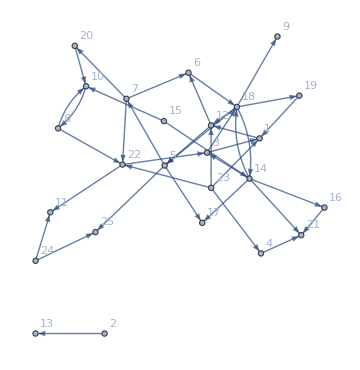

```mathematica
G=RandomGraph[{25,40},DirectedEdges-> True,VertexLabels->"Name",ImageSize->Medium]
```

```mathematica
DFSearch[G]
BFSearch[G]
DDVertex[G]
```

{1,12,5,6,7,17,25,20,22,18,9,14,19,3,16,21,10,8,11,2,13,4,15,23,24}

{1,12,5,6,7,17,25,18,20,22,9,14,19,10,3,11,16,21,8,2,13,4,15,23,24}

{18,14,23,7,5,24,22,15,12,8,3,20,19,16,10,6,4,2,1,25,21,17,13,11,9}

{{1->12,2->13,5->7,5->17,5->25,6->18,7->20,7->22,10->8,12->5,12->6,14->3,14->16,14->21,16->21,18->9,18->14,18->19,20->10,22->3,22->11}→Ациклический граф,{3->1,3->18,4->21,7->6,8->10,8->22,14->17,14->18,15->10,15->14,18->5,18->12,19->1,23->1,23->4,23->12,23->22,24->11,24->25}→Feedback Set}

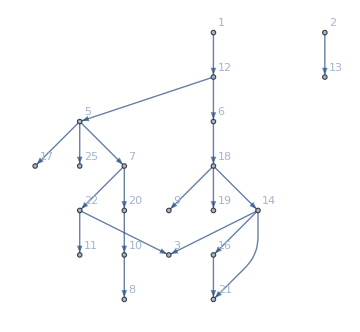

```mathematica
{acy, fs} = acANDfs[G,DFSearch]
Graph[acy⟦1⟧,DirectedEdges-> True,VertexLabels->"Name",ImageSize->Medium]
```

```mathematica
{acy, fs} = acANDfs[G,BFSearch]
Graph[acy⟦1⟧,DirectedEdges-> True,VertexLabels->"Name",ImageSize->Medium]
```

{{1->12,2->13,5->7,5->17,5->25,6->18,7->20,7->22,10->8,12->5,12->6,14->3,14->16,14->21,16->21,18->9,18->14,18->19,20->10,22->3,22->11}→Ациклический граф,{3->1,3->18,4->21,7->6,8->10,8->22,14->17,14->18,15->10,15->14,18->5,18->12,19->1,23->1,23->4,23->12,23->22,24->11,24->25}→Feedback Set}

-Graphics-

{{2->13,3->1,4->21,5->17,5->25,7->6,7->20,7->22,8->10,12->6,14->3,14->16,14->17,14->21,15->10,16->21,18->5,18->9,18->12,18->14,18->19,19->1,20->10,22->3,22->11,23->1,23->4,23->12,23->22,24->11,24->25}→Ациклический граф,{1->12,3->18,5->7,6->18,8->22,10->8,12->5,14->18,15->14}→Feedback Set}

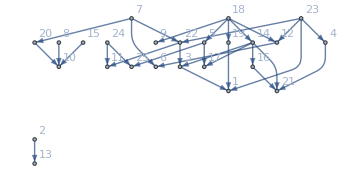

```mathematica
{acy, fs} = acANDfs[G,DDVertex]
Graph[acy⟦1⟧,DirectedEdges-> True,VertexLabels->"Name",ImageSize->Medium]
```

## 2. Greedy Cycle Removal

## 2.1 Постановка задачи

Реализовать алгоритм Greedy Cycle Removal. На выходе получить ациклический граф и множество Feedback Set.

d^+(w) - количество рёбер, исходящих из вершины w
d^-(w) - количество рёбер, входящих в вершину w
Sink - ребро, не имеющее выхода из себя, d^+(w) = 0
Source - ребро, не имеющее входа в себя, d^-(w) = 0
Алгоритм, как я понял, следующий: 
1. убираем все Sink вершины
2. убираем все Source вершины
3. Пока граф не становится пустым:
	- выбираем ту вершину, имеющую d^+(w) - d^-(w)→max
	- удаляем из графа данную вершину w
	- добавляем в конец списка S_L
Попытался реализовать в соответствии с псевдокодом.

## 2.2 Реализация

```mathematica
Clear[sinkV,sourceV,GreedyCycleRemoval]
sinkV[g_?GraphQ]:=Pick[VertexList[g],VertexOutDegree[g],False]
sourceV[g_?GraphQ]:=Pick[VertexList[g],VertexInDegree[g],False]
GreedyCycleRemoval[g_?GraphQ]:=
Module[{sl={},sr={},G=g,sinks,sources,w},
While[
EmptyGraphQ[G]==False,
sinks=sinkV[G];
While[sinks!={},
	G=VertexDelete[G,sinks];
	PrependTo[sr,sinks];
	sinks=sinkV[G];
	];
sources=sourceV[G];
While[sources!={},
	G=VertexDelete[G,sources];
	AppendTo[sl,sources];
	sources=sourceV[G];
	];
If[EmptyGraphQ[G]==False,
	w =First[Keys[ReverseSort[Association[Thread[VertexList[G]->Table[VertexOutDegree[G,v]-VertexInDegree[G,v],{v,VertexList[G]}]]]]]];
	G=VertexDelete[G,w];
	AppendTo[sl,w];
	]
	];
Flatten[sl]~Join~Flatten[sr]
]
```

## 2.3 Test

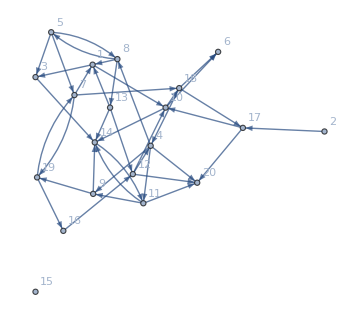

```mathematica
G=RandomGraph[{20,40},DirectedEdges-> True,VertexLabels->"Name",ImageSize->Medium]
```

{{1->3,1->10,2->17,3->14,4->8,4->9,4->11,4->20,5->3,5->7,5->8,7->1,7->18,7->19,8->1,9->14,9->19,10->6,10->14,11->9,11->14,11->20,12->10,12->20,13->1,13->12,13->14,16->12,17->10,17->20,18->4,18->6,18->17,19->16}→Ациклический граф,{8->5,8->13,10->18,12->4,14->11,19->7}→Feedback Set}

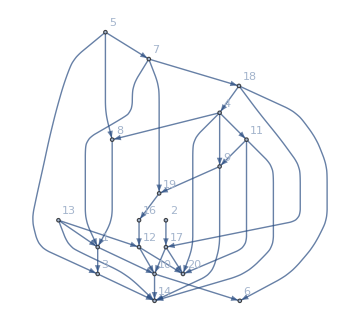

```mathematica
{acy, fs} = acANDfs[G,GreedyCycleRemoval]
Graph[acy⟦1⟧,DirectedEdges-> True,VertexLabels->"Name",ImageSize->Medium]
```